# Visualizing Normalization

## A graphical presentation of NMR normalization methods.

Eric Moyer

Started 27 May 2012

## Introduction

Normalization methods in NMR spectrography (and probably other spectrographic fields as well) are typically explained by the procedures that you go through to perform them and justified by arguments about the "real concentration." Another way to look at normalization methods is to examine them as geometric operations on a vector space. This gives a different understanding of what is occurring, which can give the practitioner a deeper intuition about trade-offs he makes when he says, "sum-normalize the data."

I look at each spectrum generated as a point in a vector space, one variable in the vector for each value measured. I am mainly concerned with frequency-domain spectra, since it is on these that the normalization methods I present are typically used. The normalization methods do not solve extant problems on time-domain spectra, so they are not used there. However, my points are just as valid for time-domain spectra, since they too are vectors.

## Sum Normalization

Sum normalization takes each spectrum, divides it by its sum, and then multiplies it by a constant. After this operation, all spectra have the same sum.

If the spectra are interpreted as points in an n-dimensional vector space, this projects all points onto (a set of) n-1 dimensional subspaces (hyperplanes) along a line between the original point and the origin. In 3 dimensions, it projects points onto 8 planes forming an octahedron about the origin. In 2 dimensions, all points are projected onto a square rotated  90-degrees. The size of these figures is determined by the constant.

How can we see this?

First, consider that multiplying a (non-zero) point by a constant moves it along a line connecting the point with the origin. Multiplying by a positive number less than 1 moves it closer to the origin. Multiplying by a number greater than 1 moves farther from the origin. And multiplying it by a negative number moves it away from the origin on the opposite side.

```mathematica
xPlusYEq1TwoD=Show[Plot[{1-x,x-1},{x,0,1},PlotStyle->Red],Plot[{x+1,-1-x},{x,-1,0},PlotStyle->Red],PlotRange->{-1,1}];
```

```mathematica
yEq2X=Plot[{2x},{x,0,3/2},PlotStyle->Darker[Blue]];
```

```mathematica
ptX3HalvesY3AndProjection=ListPlot[{{{3/2,3}},{{1/3,2/3}}},PlotMarkers->{Automatic,Medium},PlotStyle->{Darker[Blue],Darker[Magenta]}];
```

```mathematica
firstDiagram=Show[{xPlusYEq1TwoD,Graphics[{Text["Constant sum surface",{5/8,-1/2},{-1,0},BaseStyle->{Red}],Text["Spectrum",{3/2,11/4},{-1,0},BaseStyle->{Darker[Blue]}]}],yEq2X,ptX3HalvesY3AndProjection},PlotRange->All,AspectRatio->Automatic,ImageSize->{300},PlotRangeClipping->False];
```

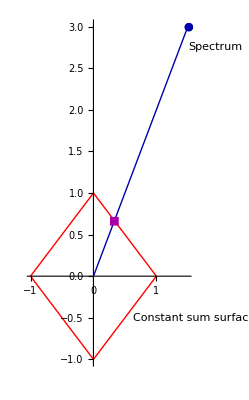
-Graphics-Figure 1: Sum Normalization in Two Dimensions

```mathematica
firstDiagramWithCaption=Labeled[firstDiagram,"Figure 1: Sum Normalization in Two Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

The point at which the line through the origin intersects with the surface of points whose sum equals the target sum of the sum-normalization is the normalized point. Figures 1 and 2 show sum-normalization in two and three dimensions with a target sum of 1.

```mathematica
quarterOctahedron=Polygon[{{{0,0,1},{0,1,0},{1,0,0}},{{0,0,-1},{0,1,0},{1,0,0}}}];
```

```mathematica
sumEq1ThreeD=Graphics3D[{Opacity[0.85],Red,quarterOctahedron,Rotate[quarterOctahedron,Pi/2,{0,0,1}],Rotate[quarterOctahedron,Pi,{0,0,1}],Rotate[quarterOctahedron,3Pi/2,{0,0,1}]},Axes->True,Lighting->"Neutral"];
```

```mathematica
yEq2XThreeD=Graphics3D[{Darker[Blue],Line[{{0,0,0},{3/2,0,3}}],PointSize[Large],Point[{3/2,0,3}],Darker[Magenta],Point[{1/3,0,2/3}]}];
```

```mathematica
secondDiagram=Show[{sumEq1ThreeD,yEq2XThreeD}];
```

```mathematica
secondDiagramWithCaption=Labeled[secondDiagram,"Figure 2: Sum Normalization in Three Dimensions",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics3D-Figure 2: Sum Normalization in Three Dimensions

## Probabilistic Quotient Normalization

Probabilistic Quotient Normalization (PQN) (Dieterle 2006) is a method that is more resistant to large fluctuations in parts of the spectrum due to factors other than dilution (such as treatments). Unlike sum-normalization, which normalizes each spectrum independently, PQN is designed to normalize several related spectra simultaneously, using their commonality to improve its estimates.

PQN starts with sum-normalization. Next, the spectra are binned to take care of small peak-shifts. Then a reference spectrum is created. The original paper mentions several methods of creating reference spectra. However, for simplicity, we will choose the method that takes the median spectrum of all the spectra being analyzed. Then, for each spectrum to be normalized, the reference spectrum is divided by it and the median of the quotients is selected as the normalization factor. Finally the spectra are multiplied by their respective normalization factors.

For the following discussion, we will assume that the initial spectra have no negative values. Negative values result from noise or special acquisition methods like dephasing the water signal and should be removed during preprocessing. Though PQN is well-defined with negative values, their inclusion unnecessarily complicates the explanation.

### 2D PQN (the canonical way)

#### Sum Normalize

The first step of PQN we've seen before, we sum-normalize. In the diagrams, I sum-normalize to 1, since it is easy, but everything works out the same, just scaled a bit differently if you sum-normalize to a different constant.

```mathematica
orig2D={{2.172454345958343,1.7744919345405104},{2.675301724350803,1.359406145521423},{2.87830990460933,1.4709889319173473},{2.8813454193984884,1.073276896492814},{2.3606473361385762,1.7882842580601983},{2.26005835257858,1.7655977040112563},{1.398151988227432,2.097238014713233},{3.0861624358478528,0.9274842729247682},{2.255768229218814,1.8706253682049265},{2.6917625635090703,1.2898265639379862}};
```

```mathematica
sumNorm2D=Map[#/Total[#]&,orig2D];
```

```mathematica
thirdDiagram=Graphics[{PointSize->Medium,Darker[Blue],Map[Point[#]&,orig2D],Map[Line[{{0,0},#}]&,orig2D],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}]},Axes->True];
```

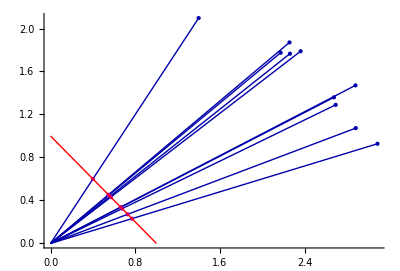
-Graphics-Figure 3: First step of 2D PQN: Sum-Normalize

```mathematica
thirdDiagramWithCaption=Labeled[thirdDiagram,"Figure 3: First step of 2D PQN: Sum-Normalize",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Reference Spectrum

Next, you generate a reference spectrum by taking the median of each variable.

```mathematica
refPt2D=Map[Median,Transpose[sumNorm2D]]
```

{0.615382,0.384618}

```mathematica
fourthDiagram=Graphics[{PointSize[Medium],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}],Green,PointSize[Large],Point[refPt2D],Text["Reference spectrum",{0.025,0}+refPt2D,{-1,0}]},Axes->True];
```

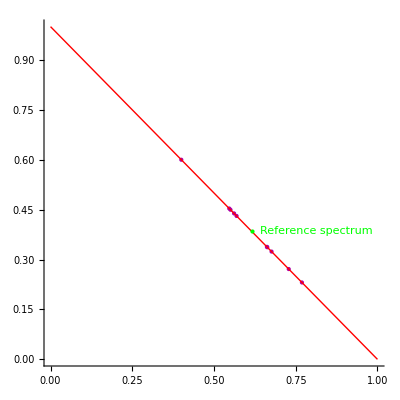
-Graphics-Figure 4: Second step of 2D PQN: Create reference spectrum

```mathematica
fourthDiagramWithCaption=Labeled[fourthDiagram,"Figure 4: Second step of 2D PQN: Create reference spectrum",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Reciprocal Quotient Spectra

In the next step, I make a change to the procedure that makes it easier to understand. Rather than dividing the reference spectrum by each of the individual spectra to get the quotient spectra, I divide each spectrum by the reference spectrum. This leaves me with quotient spectra that have the reciprocals of the proper coordinates. Because all of the individual coordinates are positive, this just reverses their ranks. The median element will still be the same. So, I can just divide by the median rather than multiplying to get the same final normalization.

```mathematica
standardQuotientTransformPlot=ParametricPlot[{{t,1-t},{refPt2D[[1]]/t,refPt2D[[2]]/(1-t)}},{t,0.001,1},AspectRatio->Automatic,PlotRange->{{0,3},{0,3}},ColorFunction->Function[{x,y,u},Hue[u/1.1]],PlotStyle->Thickness[0.025]];
```

```mathematica
standardQuotientArrows=Graphics[{Thickness[Small],Flatten[Map[{Hue[#],Arrow[{{#,1-#},{refPt2D[[1]]/#,refPt2D[[2]]/(1-#)}},{0,.9Abs[refPt2D[[1]]-#]}]}&,refPt2D[[1]]+{-0.15,-0.06,0.06,0.15}]]}];
```

```mathematica
fifthDiagram=Show[{standardQuotientTransformPlot,standardQuotientArrows,Graphics[{Text["Sum-normalized spectra",{1,0.2},{-1,0}],Text["Quotient spectra using standard method",{.7,2.5},{-1,0}],Text["Colors give correspondence (note reversal)",{0.7,2.36},{-1,0}] }]}];
```

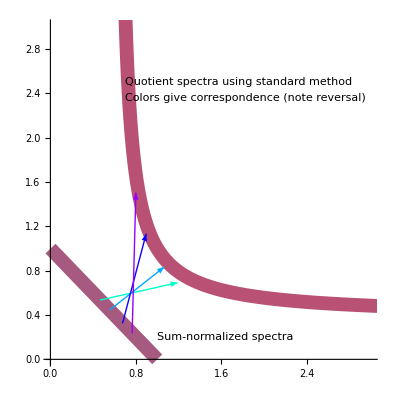
-Graphics-Figure 5: Standard method of creating quotient spectra

```mathematica
fifthDiagramWithCaption=Labeled[fifthDiagram,"Figure 5: Standard method of creating quotient spectra",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

```mathematica
linearQuotientTransformPlot=ParametricPlot[{{t,1-t},{t/refPt2D[[1]],(1-t)/refPt2D[[2]]}},{t,0.001,1},AspectRatio->Automatic,PlotRange->{{0,3},{0,3}},ColorFunction->Function[{x,y,u},Hue[u/1.1]],PlotStyle->Thickness[0.025]];
```

```mathematica
linearQuotientArrows=Graphics[{Thickness[Small],Flatten[Map[{Hue[#],Arrow[{{#,1-#},{#/refPt2D[[1]],(1-#)/refPt2D[[2]]}},0.1]}&,refPt2D[[1]]+{-.25,-0.15,-0.06,0.06,0.15,0.25}]]}];
```

```mathematica
sixthDiagram=Show[{linearQuotientTransformPlot,linearQuotientArrows,Graphics[{Text["Sum-normalized",{.9,0.2},{-1,0}],Text["Reciprocal Quotient spectra",{.3,1.89},{-1,0}],Text["Colors give correspondence",{0.3,1.75},{-1,0}] }]}];
```

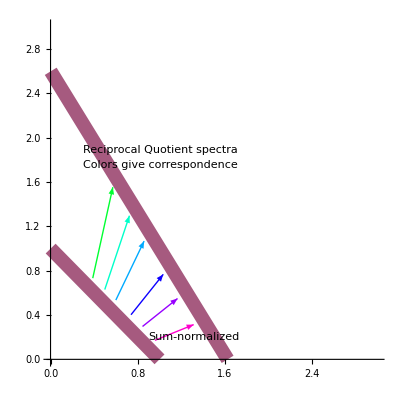
-Graphics-Figure 6: Easy-to-visualize method of creating reciprocal quotient spectra

```mathematica
sixthDiagramWithCaption=Labeled[sixthDiagram,"Figure 6: Easy-to-visualize method of creating reciprocal quotient spectra",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

The standard method involves three non-linear transformations of the spectral space, one to create the quotient spectra and then another to extract their medians, and a third to multiply the corresponding spectra by their medians. My method involves only two non-linear transformations - extracting the medians and dividing by them. The creation of the reciprocal quotient  (r-quotient) spectra is a linear transformation. Further, my method of creating the quotients does not flip the axes. This makes my method much easier to visualize. You can compare the two methods of creating the quotient spectra by looking at figures 5 and 6 (these diagrams are created using the reference spectrum from figure 4).

#### Median Reciprocal Quotients

After generating the r-quotient spectra, the next step is to take the median of the r-quotients, that is, the median of all of the coordinates of each spectrum. For the two-dimensional case, this is particularly simple. The median of two numbers is just their mean. So, the points on a line (x, m x+b) become q=(x+m x+b)/2=(m+1)/2 x+b/2,  another line. Since m, the slope of the original line, must be negative, the resulting line has a positive slope if and only if |m|<1 and the new positive slope will be less than 1/2 because m<0⇒(m+1)/2<1/2.

```mathematica
linearQuotientAlonePlot=ParametricPlot[{{t/refPt2D[[1]],(1-t)/refPt2D[[2]]}},{t,0,1},AspectRatio->Automatic,PlotRange->{{0,2.5},{0,3.5}},ColorFunction->Function[{x,y,u},Hue[u/1.1]],PlotStyle->Thickness[0.0125]];
```

```mathematica
quotientLineLeftEndpoint={0,1/refPt2D[[2]]};
```

```mathematica
quotientLineRightEndpoint={1/refPt2D[[1]],0};
```

```mathematica
quotientLineUnitNormal=Reverse[Normalize[quotientLineRightEndpoint-quotientLineLeftEndpoint]]{-1,1};
```

```mathematica
quotientPolygon=Graphics[{Gray,Polygon[{quotientLineLeftEndpoint,quotientLineRightEndpoint,quotientLineRightEndpoint+Median[quotientLineRightEndpoint] quotientLineUnitNormal,quotientLineLeftEndpoint+Median[quotientLineLeftEndpoint]quotientLineUnitNormal}]}];
```

```mathematica
seventhDiagram=Show[quotientPolygon,linearQuotientAlonePlot,Options[linearQuotientAlonePlot]];
```

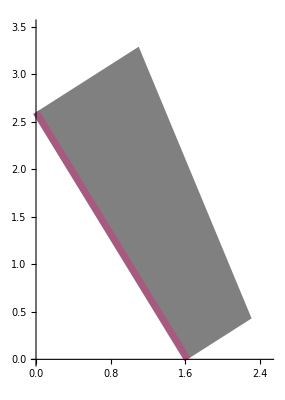
-Graphics-Figure 7: Median r-quotient in gray as distance perpendicular to r-quotient line.

```mathematica
seventhDiagramWithCaption=Labeled[seventhDiagram,"Figure 7: Median r-quotient in gray as distance perpendicular to r-quotient line. ",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

##### Digression on slope of median r-quotient line

It is interesting to consider a few more constraints on the slope of the median r-quotient line. In the two-dimensional case with positive coordinates in the original spectra, the reference spectrum must also be sum-normalized. This is because the x coordinates of the normalized spectra will be between 0 and the target sum. The y coordinates will then be just the x coordinates subtracted from the target sum. If you order the points by x coordinate, the y coordinates will be in reverse order. The same point (or pair of points) will fall in the middle of both sequences. Thus the median coordinates will be either the coordinates of one of the normalized spectra, if there are an odd number of points, and thus be normalized. Or they will be the mean of the coordinates of two points. Since both points lie on the same line, their mean does too. So, in the case of an even number of spectra, the reference spectrum will still be normalized.

That the reference spectrum is normalized means that it is a pair (r,1-r). For clarity, I will just speak of the case where the target sum is 1 and assume r≠1 and r≠0. Then the line containing the r-quotient spectra is the line running through the two points (1/r,0) and (0,1/(1-r)). Thus, the r-quotient spectra line is y=r/(r-1)x+1/(1-r). The slope of the line containing the median r-quotient is then (r/(r-1)+1)/2=r/(2(r-1))+1/2=(r+r-1)/(2(r-1))=(2r-1)/(2r-2). Figure 8 graphs this function.

```mathematica
eighthDiagram=Plot[{(2r-1)/(2(r-1))},{r,0,1},AxesLabel->{"r","Slope of median-line"}];
```

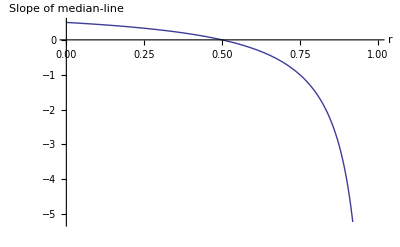
-Graphics-Figure 8: Slope of line containing the median reciprocal quotients as a function of the x coordinate of the reference spectrum

```mathematica
eighthDiagramWithCaption=Labeled[eighthDiagram,"Figure 8: Slope of line containing the median reciprocal quotients as a function of the x coordinate of the reference spectrum",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Move Median R-Quotients

The median r-quotients in the previous step are displayed attached to their corresponding reciprocal quotient points. But they should be attached to the sum-normalized points. The next step matches the median quotients back to the original points.

```mathematica
scaledQuotientPolygon=Graphics[{Gray,Polygon[{{1,0},{0,1},{0,1}+Median[quotientLineLeftEndpoint]{1,1},{1,0}+Median[quotientLineRightEndpoint] {1,1}}]}];
```

```mathematica
sumNormPointsPlot=Graphics[{PointSize[Medium],Darker[Magenta],Map[Point[#]&,sumNorm2D],Red,Line[{{1,0},{0,1}}]},Axes->True];
```

```mathematica
ninthDiagram=Show[scaledQuotientPolygon,sumNormPointsPlot,Options[sumNormPointsPlot]];
```

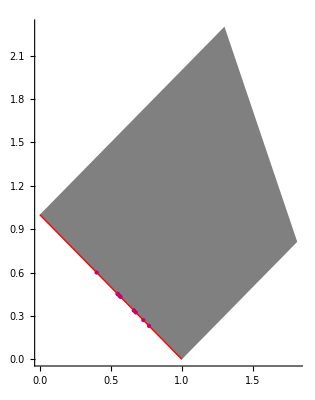
-Graphics-Figure 9: Sum-normalized points with their r-quotient scaling factors above them.

```mathematica
ninthDiagramWithCaption=Labeled[ninthDiagram,"Figure 9: Sum-normalized points with their r-quotient scaling factors above them.",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

#### Scale Sum-Normalized Points

The final step is to divide each spectrum by its corresponding reciprocal quotient.

```mathematica
rQuotientForX2D[x_,refPt_]:=With[{xQuot=x/refPt[[1]],yQuot=(1-x)/refPt[[2]]},
(xQuot+yQuot)/2]
```

### 2D PQN (the easy way)

Because 2D is such a special case (the median is the same as the mean and the reference spectrum can be specified by one variable), the entire normalization procedure can be viewed in two simple steps. First, sum normalize as before and choose the reference spectrum.

```mathematica
eleventhDiagramWithCaption=Labeled[fourthDiagram,"Figure 11: Points sum-normalized with reference spectrum",Bottom,LabelStyle->Directive[Bold,FontFamily->Times]]
```

-Graphics-Figure 11: Points sum-normalized with reference spectrum

For any point sum-normalized to the coordinates, (x_sn,1-x_sn) and when the reference spectrum is (r,1-r), the r-quotient is 1/2((1-x_sn)/(1-r)+x_sn/r)which makes the normalization factor ((2 r-2) r)/(x_sn(2 r-1)-r).

This means that the final coordinates are x=-(2 (-1+r) r x_sn)/(r+x_sn-2 r x_sn) and y=-(2 (-1+r) r (-1+x_sn))/(-x_sn+r (-1+2 x_sn)). When we eliminate x_sn, we arrive at a line: y=(r-1)/r x+2(1-r). Noting that 1-r is the y coordinate of the reference point, we can rewrite this as:

y=2 r_y-r_y/r_x x

This is the line between the two points (0, 2 r_y) and (2 r_x,0). The final scaled points are just the intersections between this line and the lines to the original points. Thus, in two dimensions, when all spectra have only positive coordinates, we can look at PQN as just replacing the sum normalization line y=1-x with the line y=2 r_y-r_y/r_x x derived from the reference spectrum. This is easiest to visualize if we imagine sum-normalizing to 2 rather than 1 and then producing the line directly from the coordinates of the reference point.

```mathematica
pqn2D[point_,refPt_]:=With[{t=point[[1]]/Total[point],r=refPt[[1]]},{-(2 (-1+r) r t)/(r+t-2 r t),-(2 (-1+r) r (-1+t))/(-t+r (-1+2 t))}]
```

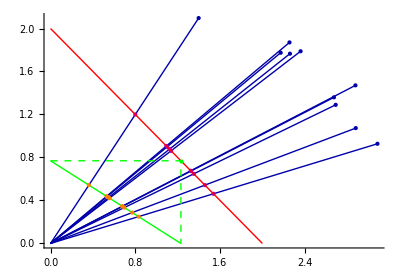

```mathematica
twelfthDiagram=Graphics[{PointSize->Medium,Darker[Blue],Map[Point[#]&,orig2D],Map[Line[{{0,0},#}]&,orig2D],Darker[Magenta],Map[Point[#]&,2sumNorm2D],Red,Line[{{2,0},{0,2}}],PointSize[Medium],Green,Point[2 refPt2D],Line[{{0,2refPt2D[[2]]},{2refPt2D[[1]],0}}],Dashed,Line[{{0,2refPt2D[[2]]},2refPt2D,{2refPt2D[[1]],0}}],Orange,Map[Point[pqn2D[#,refPt2D]]&,orig2D]},Axes->True]
```

```mathematica
shifted2D=Map[With[{sn=2#/Total[#]},With[{sh=sn+{-0.2,0.2}},sh Total[#]/2]]&,orig2D]
```

{{2.17245,1.77449},{2.6753,1.35941},{2.87831,1.47099},{2.88135,1.07328},{2.36065,1.78828},{2.26006,1.7656},{1.39815,2.09724},{3.08616,0.927484},{2.25577,1.87063},{2.69176,1.28983}}

```mathematica
shiftedSumNorm2D=Map[#/Total[#]&,shifted2D];
```

```mathematica
shiftedRef2D=Map[Median,Transpose[shiftedSumNorm2D]]
```

{0.615382,0.384618}

```mathematica
twelfthDiagram=Graphics[{PointSize->Medium,Darker[Blue],Map[Point[#]&,shifted2D],Map[Line[{{0,0},#}]&,shifted2D],Darker[Magenta],Map[Point[#]&,2shiftedSumNorm2D],Red,Line[{{2,0},{0,2}}],PointSize[Medium],Green,Point[2 shiftedRef2D],Line[{{0,2shiftedRef2D[[2]]},{2shiftedRef2D[[1]],0}}],Dashed,Line[{{0,2shiftedRef2D[[2]]},2shiftedRef2D,{2shiftedRef2D[[1]],0}}],Orange,Map[Point[pqn2D[#,shiftedRef2D]]&,shifted2D]},Axes->True]
```

-Graphics-

```mathematica
Solve[0==2 ry-ry/rx x,{x}]
```

{{x→2 rx}}

```mathematica
rQuotientForX2D[t,{r,1-r}]/.t->Subscript[x, sn]
```

1/2 ((1-x_sn)/(1-r)+x_sn/r)

```mathematica
FullSimplify[1/rQuotientForX2D[t,{r,1-r}]]/.t->Subscript[x, sn]
```

-(2 (-1+r) r)/(r+x_sn-2 r x_sn)

```mathematica
Simplify[(1-t)/rQuotientForX2D[t,{r,1-r}]]
```

-(2 (-1+r) r (-1+t))/(-t+r (-1+2 t))

```mathematica
Simplify[t/rQuotientForX2D[t,{r,1-r}]]/.t->Subscript[x, sn]
```

-(2 (-1+r) r x_sn)/(r+x_sn-2 r x_sn)

```mathematica
Simplify[(1-t)/rQuotientForX2D[t,{r,1-r}]]/.t->Subscript[x, sn]
```

-(2 (-1+r) r (-1+x_sn))/(-x_sn+r (-1+2 x_sn))

```mathematica
FullSimplify[Solve[x==FullSimplify[(x/.Solve[{x==-(2 (-1+a) a t)/(a+t-2 a t),y==-(2 (-1+a) a (-1+t))/(-t+a (-1+2 t))},{x,y},{t}])[[1]]]/.a->r,{y}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→2-2 r+x-x/r}}